# 500kHz

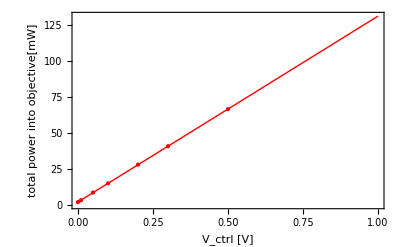

```mathematica
data=Thread[{{0,0.01,0.05,0.1,0.2,0.5,0.3},{1,1.65,4.3,7.5,14,33.3,20.4}2}];
fitfn=a x+ b;
fit=FindFit[data,fitfn,{a,b},x];
Show[
{
Plot[fitfn/.fit,{x,0,1},Axes->False,Frame->True,FrameLabel->{"V_ctrl [V]","total power into objective[mW]",fitfn/.fit}],
ListPlot[data]
}
]
```

```mathematica
Vctrl=0.5;
(*total power in mW going into tweezer *)
ToString[fitfn/.fit/.x->Vctrl]<>" mW total"
(*gnd state trap depth in mK *)
ToString[0.26 fitfn/.fit/.x->Vctrl]<>" mK gnd state trap depth"
(*light shift in MHz *)
ToString[4.2 fitfn/.fit/.x->Vctrl]<>" MHz shift"
```

66.6414 mW total

17.3268 mK gnd state trap depth

279.894 MHz shift